```mathematica
Impact[{R1,R2},n1]
```

```mathematica
{D[dR1/.EcoEvo`Private`RemoveVariablets,n1],D[dR2/.EcoEvo`Private`RemoveVariablets,n1]}
```

{-2 Min[R1/2,2. R2],-0.5 Min[R1/2,2. R2]}

```mathematica
?VectorPlot
```

```mathematica
EcoEvo`Private`auxeqn[R1]
```

EcoEvo`Private`auxeqn[R1]

```mathematica
ImpactVector[{var1_,var2_},sp_]:=D[{EcoEvo`Private`eqn[var1],EcoEvo`Private`eqn[var2]}/.EcoEvo`Private`RemoveVariablets,sp]
```

```mathematica
ImpactVector[{R1,R2},n1]/.{R1->1,R2->1}
```

{-1,-2}

```mathematica
ImpactVector[{R1,R2},n2]/.{R1->1,R2->1}
```

{-2,-1}

```mathematica
ImpactVector[{R1,R2},n2]/.{R1->1,R2->1}
```

{-2,-1}

```mathematica
PlotImpactVector[{var1_,var2_},sp_,point_]:=Graphics[{EcoEvo`Private`color[sp],Arrow[{{var1,var2},{var1,var2}+0.5*Normalize@ImpactVector[{var1,var2},sp]}/.point]}]
```

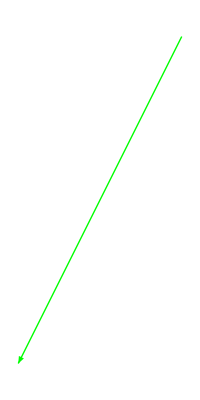

```mathematica
PlotImpactVector[{R1,R2},n1,{R1->1,R2->1}]
```